# CNN Project

## Review

Baoxiang Pan
2017.7.13

## Data

```mathematica
SetDirectory["/Users/lambda/Documents/Data/CPC_Precipitation"];
year=1948;
data=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}][[;;,48;;,21;;65]];
data[[;;,32;;,26;;]]=nan;
Block[{grid=Flatten[Table[Table[{i,j},{i,34.125,39.125+0.25,0.25}],{j,240.125,246.125,0.25}],1],t,tt},
	t=Select[grid,#[[1]]-34+6/5*(#[[2]]-246)>0&];
	tt=Map[{Position[mlat,#[[1]]][[1,1]],Position[mlon,#[[2]]][[1,1]]}&,t];
	Map[Set[data[[;;,#[[1]],#[[2]]]],nan]&,tt]];
lat=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lat"}];
lon=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","lon"}];
```

```mathematica
mlat=lat[[48;;]];
mlon=lon[[21;;65]];
```

```mathematica
FullForm[Delayed[x=1]]
```

Delayed[Set[x,1]]

```mathematica
Dimensions[data]
```

{366,73,45}

```mathematica
Dimensions[tt]
```

{204,2}

```mathematica
Map[data[[;; #[[1]], #[[2]]]] = 0 &, tt];
```

Part::partw: Part 2 of #1 does not exist.

Set::pkspec1: The expression #1⟦2⟧ cannot be used as a part specification.

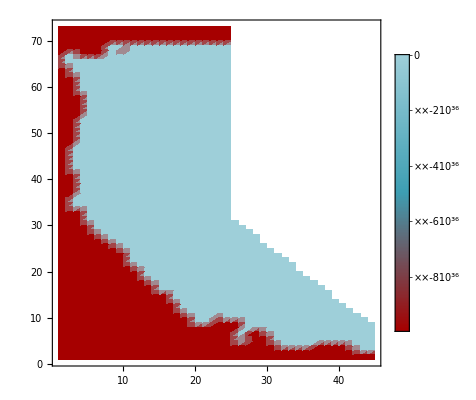

```mathematica
ListDensityPlot[data[[1,;;,;;]],PlotLegends->Automatic,PlotRange->Full]
```

```mathematica
test={{1,2,3},{4,5,1},{5,6,3}}
```

{{1,2,3},{4,5,1},{5,6,3}}

```mathematica
test
```

{{1,2,3},{4,5,1},{5,6,3}}

```mathematica
FullForm[Delayed[test /. 3->1]]
```

Delayed[ReplaceAll[test,Rule[3,1]]]

```mathematica
test /. x_/; x< 5 ->1.2
```

{{1.2,1.2,1.2},{1.2,5,1.2},{5,6,1.2}}

```mathematica
FullForm[Delayed[test /. x_ /; x < 5 -> 0]]
```

Delayed[ReplaceAll[test,Rule[Condition[Pattern[x,Blank[]],Less[x,5]],0]]]

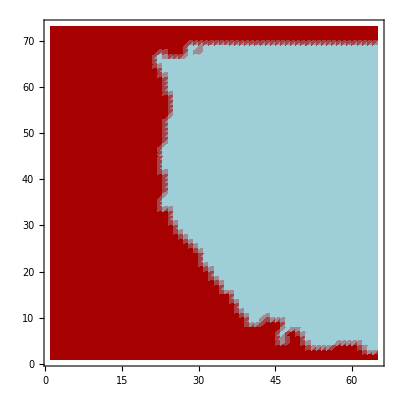

```mathematica
ListDensityPlot[data[[1,;;,;;]]]
```

```mathematica
lat
```

{20.125,20.375,20.625,20.875,21.125,21.375,21.625,21.875,22.125,22.375,22.625,22.875,23.125,23.375,23.625,23.875,24.125,24.375,24.625,24.875,25.125,25.375,25.625,25.875,26.125,26.375,26.625,26.875,27.125,27.375,27.625,27.875,28.125,28.375,28.625,28.875,29.125,29.375,29.625,29.875,30.125,30.375,30.625,30.875,31.125,31.375,31.625,31.875,32.125,32.375,32.625,32.875,33.125,33.375,33.625,33.875,34.125,34.375,34.625,34.875,35.125,35.375,35.625,35.875,36.125,36.375,36.625,36.875,37.125,37.375,37.625,37.875,38.125,38.375,38.625,38.875,39.125,39.375,39.625,39.875,40.125,40.375,40.625,40.875,41.125,41.375,41.625,41.875,42.125,42.375,42.625,42.875,43.125,43.375,43.625,43.875,44.125,44.375,44.625,44.875,45.125,45.375,45.625,45.875,46.125,46.375,46.625,46.875,47.125,47.375,47.625,47.875,48.125,48.375,48.625,48.875,49.125,49.375,49.625,49.875}

```mathematica
Position[lat,31.875]
```

{{48}}

```mathematica
Position[lon,246.125]
```

{{65}}

```mathematica
lon
```

{230.125,230.375,230.625,230.875,231.125,231.375,231.625,231.875,232.125,232.375,232.625,232.875,233.125,233.375,233.625,233.875,234.125,234.375,234.625,234.875,235.125,235.375,235.625,235.875,236.125,236.375,236.625,236.875,237.125,237.375,237.625,237.875,238.125,238.375,238.625,238.875,239.125,239.375,239.625,239.875,240.125,240.375,240.625,240.875,241.125,241.375,241.625,241.875,242.125,242.375,242.625,242.875,243.125,243.375,243.625,243.875,244.125,244.375,244.625,244.875,245.125,245.375,245.625,245.875,246.125,246.375,246.625,246.875,247.125,247.375,247.625,247.875,248.125,248.375,248.625,248.875,249.125,249.375,249.625,249.875,250.125,250.375,250.625,250.875,251.125,251.375,251.625,251.875,252.125,252.375,252.625,252.875,253.125,253.375,253.625,253.875,254.125,254.375,254.625,254.875,255.125,255.375,255.625,255.875,256.125,256.375,256.625,256.875,257.125,257.375,257.625,257.875,258.125,258.375,258.625,258.875,259.125,259.375,259.625,259.875,260.125,260.375,260.625,260.875,261.125,261.375,261.625,261.875,262.125,262.375,262.625,262.875,263.125,263.375,263.625,263.875,264.125,264.375,264.625,264.875,265.125,265.375,265.625,265.875,266.125,266.375,266.625,266.875,267.125,267.375,267.625,267.875,268.125,268.375,268.625,268.875,269.125,269.375,269.625,269.875,270.125,270.375,270.625,270.875,271.125,271.375,271.625,271.875,272.125,272.375,272.625,272.875,273.125,273.375,273.625,273.875,274.125,274.375,274.625,274.875,275.125,275.375,275.625,275.875,276.125,276.375,276.625,276.875,277.125,277.375,277.625,277.875,278.125,278.375,278.625,278.875,279.125,279.375,279.625,279.875,280.125,280.375,280.625,280.875,281.125,281.375,281.625,281.875,282.125,282.375,282.625,282.875,283.125,283.375,283.625,283.875,284.125,284.375,284.625,284.875,285.125,285.375,285.625,285.875,286.125,286.375,286.625,286.875,287.125,287.375,287.625,287.875,288.125,288.375,288.625,288.875,289.125,289.375,289.625,289.875,290.125,290.375,290.625,290.875,291.125,291.375,291.625,291.875,292.125,292.375,292.625,292.875,293.125,293.375,293.625,293.875,294.125,294.375,294.625,294.875,295.125,295.375,295.625,295.875,296.125,296.375,296.625,296.875,297.125,297.375,297.625,297.875,298.125,298.375,298.625,298.875,299.125,299.375,299.625,299.875,300.125,300.375,300.625,300.875,301.125,301.375,301.625,301.875,302.125,302.375,302.625,302.875,303.125,303.375,303.625,303.875,304.125,304.375,304.625,304.875}

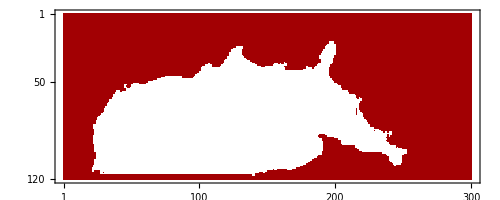

```mathematica
MatrixPlot[data[[3,;;,;;]]]
```

```mathematica
precipitation=Table[Block[{data},
	data=Import["precip.V1.0."<>ToString[year]<>".nc",{"Datasets","precip"}];
```

## Network Structure

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

Item duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

Subitem nam liber tempor cum soluta nobis eleifend option congue nihil imperdiet doming id quod mazim placerat facer possim assum.

Subitem typi non habent claritatem insitam; est usus legentis in is qui facit eorum claritatem.

### Second level section heading

Text duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.

### Second level section heading

Text lorem ipsum dolor sit amet, consectetuer adipiscing elit, sed diam nonummy nibh euismod tincidunt ut laoreet dolore magna aliquam erat volutpat. Ut wisi enim ad minim veniam, quis nostrud exerci tation ullamcorper suscipit lobortis nisl ut aliquip ex ea commodo consequat.

#### Third level section heading

```mathematica
Plot[Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis]
```

-Graphics-

### Second level section heading

-Graphics- | SideCaption duis autem vel eum iriure dolor in hendrerit in vulputate velit esse molestie consequat, vel illum dolore eu feugiat nulla facilisis at vero eros et accumsan et iusto odio dignissim qui blandit praesent luptatum zril delenit augue duis dolore te feugait nulla facilisi.